## Minimal points

```mathematica
ClearAll["Global*`"]
```

### Constants

```mathematica
jconst=N[13/2];
Iconst=N[35/2];
j1axis={4.59619407771256,3.25,3.2499999999999996};
j2axis={3.2499999999999996,4.59619407771256,3.25};
j3axis={3.25,3.2499999999999996,4.59619407771256};
```

1. The classical energy function, in explicit form, using the known constants

```mathematica
en1axis[theta_,phi_]:=1/120(Iconst*Cos[theta]-j1axis[[1]])^2+1/40(Iconst*Sin[theta]*Cos[phi]-j1axis[[2]])^2+1/60(Iconst*Sin[theta]*Sin[phi]-j1axis[[3]])^2;
en2axis[theta_,phi_]:=1/120(Iconst*Sin[theta]*Sin[phi]-j2axis[[1]])^2+1/40(Iconst*Cos[theta]-j2axis[[2]])^2+1/60(Iconst*Sin[theta]*Cos[phi]-j2axis[[3]])^2;
en3axis[theta_,phi_]:=1/120(Iconst*Sin[theta]*Cos[phi]-j3axis[[1]])^2+1/40(Iconst*Sin[theta]*Sin[phi]-j3axis[[2]])^2+1/60(Iconst*Cos[theta]-j3axis[[3]])^2;
```

Numerical test of the classical energy function

```mathematica
Print[N[en1axis[1,1]]," ",N[en2axis[1,1]]," ",N[en3axis[1,1]]]
```

2.14322 1.65579 2.66717

2. The classical chiral energy function, in explicit form, using the known constants

```mathematica
enChiral1axis[theta_,phi_]:=1/120(Iconst*Cos[theta]+j1axis[[1]])^2+1/40(Iconst*Sin[theta]*Cos[phi]+j1axis[[2]])^2+1/60(Iconst*Sin[theta]*Sin[phi]+j1axis[[3]])^2;
enChiral2axis[theta_,phi_]:=1/120(Iconst*Sin[theta]*Sin[phi]+j2axis[[1]])^2+1/40(Iconst*Cos[theta]+j2axis[[2]])^2+1/60(Iconst*Sin[theta]*Cos[phi]+j2axis[[3]])^2;
enChiral3axis[theta_,phi_]:=1/120(Iconst*Sin[theta]*Cos[phi]+j3axis[[1]])^2+1/40(Iconst*Sin[theta]*Sin[phi]+j3axis[[2]])^2+1/60(Iconst*Cos[theta]+j3axis[[3]])^2;
```

Numerical test of the chiral energies

```mathematica
Print[N[enChiral1axis[1,1]]," ",N[enChiral2axis[1,1]]," ",N[enChiral3axis[1,1]]]
```

8.86242 9.06789 10.4535

## Minimization procedure for the energy function

### Helper function that extracts information from the minimization procedure

```mathematica
minpoint1axis[procedure_]:={"1-axis",Values@procedure[[2]][[1]],Values@procedure[[2]][[2]],procedure[[1]],Iconst*Cos[Values@procedure[[2]][[1]]],Iconst*Sin[Values@procedure[[2]][[1]]]*Cos[Values@procedure[[2]][[2]]],Iconst*Sin[Values@procedure[[2]][[1]]]*Sin[Values@procedure[[2]][[2]]]};
minpoint2axis[procedure_]:={"2-axis",Values@procedure[[2]][[1]],Values@procedure[[2]][[2]],procedure[[1]],Iconst*Sin[Values@procedure[[2]][[1]]]*Sin[Values@procedure[[2]][[2]]],Iconst*Cos[Values@procedure[[2]][[1]]],Iconst*Sin[Values@procedure[[2]][[1]]]*Cos[Values@procedure[[2]][[2]]]};
minpoint3axis[procedure_]:={"3-axis",Values@procedure[[2]][[1]],Values@procedure[[2]][[2]],procedure[[1]],Iconst*Sin[Values@procedure[[2]][[1]]]*Cos[Values@procedure[[2]][[2]]],Iconst*Sin[Values@procedure[[2]][[1]]]*Sin[Values@procedure[[2]][[2]]],Iconst*Cos[Values@procedure[[2]][[1]]]};
```

### Each quantization case is analyzed in terms of its contour plot behavior over the range of polar coordinates

1-axis | Energy function

```mathematica
proc11=NMinimize[{en1axis[theta,phi],0≤theta≤π,-0.5≤phi≤π},{theta,phi}];
```

1-axis | Chiral Energy function

```mathematica
procChiral11=NMinimize[{enChiral1axis[theta,phi],0≤theta≤π,-π≤phi≤-1},{theta,phi}];
procChiral12=NMinimize[{enChiral1axis[theta,phi],0≤theta≤π,1≤phi≤π},{theta,phi}];
```

2-axis | Energy function

```mathematica
proc21=NMinimize[{en2axis[theta,phi],0≤theta≤π,-π≤phi≤-0.5},{theta,phi}];
proc22=NMinimize[{en2axis[theta,phi],0≤theta≤π,0≤phi≤π},{theta,phi}];
```

2-axis | Chiral Energy function

```mathematica
procChiral21=NMinimize[{enChiral2axis[theta,phi],0≤theta≤π,-π≤phi≤-1},{theta,phi}];
procChiral22=NMinimize[{enChiral2axis[theta,phi],0≤theta≤π,1≤phi≤π},{theta,phi}];
```

3-axis | Energy function

```mathematica
proc31=NMinimize[{en3axis[theta,phi],0≤theta≤π,-0.5≤phi≤π},{theta,phi}];
```

3-axis | Chiral Energy function

```mathematica
procChiral31=NMinimize[{enChiral3axis[theta,phi],0≤theta≤π,-π≤phi≤-0.5},{theta,phi}];
procChiral32=NMinimize[{enChiral3axis[theta,phi],0≤theta≤π,1≤phi≤π},{theta,phi}];
```

```mathematica
tableNormal=Grid[{{"Minimum points\nNormal Hamiltonian",SpanFromLeft},{"Quantization axis","θ_min","φ_min","H_min(θ,φ)","I_1","I_2","I_3"},minpoint1axis[proc11],minpoint2axis[proc21],minpoint2axis[proc22],minpoint3axis[proc31]},Frame->All];
Export[StringTemplate["````.pdf"][NotebookDirectory[],"minimumPoints"],tableNormal];
```

```mathematica
tableChiral=Grid[{{"Minimum points\nChiral Hamiltonian",SpanFromLeft},{"Quantization axis","θ_min","φ_min","H_min^chiral(θ,φ)","I_1","I_2","I_3"},minpoint1axis[procChiral11],minpoint1axis[procChiral12],minpoint2axis[procChiral21],minpoint2axis[procChiral22],minpoint3axis[procChiral31],minpoint3axis[procChiral32]},Frame->All];
Export[StringTemplate["````.pdf"][NotebookDirectory[],"minimumPointsChiral"],tableChiral];
```

```mathematica
Sqrt[Sum[(minpoint1axis[proc11][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint2axis[proc21][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint2axis[proc22][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint3axis[proc31][[i+4]])^2,{i,1,3}]]
```

17.5

17.5

17.5

«1 more identical outputs»

```mathematica
Sqrt[Sum[(minpoint1axis[procChiral11][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint1axis[procChiral12][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint2axis[procChiral21][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint2axis[procChiral22][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint3axis[procChiral31][[i+4]])^2,{i,1,3}]]
Sqrt[Sum[(minpoint3axis[procChiral32][[i+4]])^2,{i,1,3}]]
```

17.5

17.5

17.5

«3 more identical outputs»

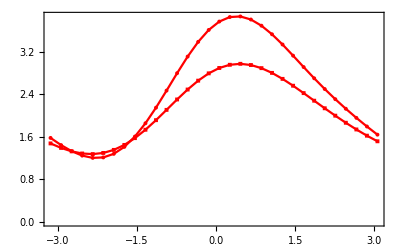

```mathematica
ListPlot[{Table[{x,enChiral1axis[2.75346,x]},{x,-π,π,0.2}],Table[{x,enChiral1axis[2.89372,x]},{x,-π,π,0.2}]},Frame->True,Axes->True,Joined->True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Red},PlotRange->Full]
```